```mathematica
<<xSSAlite.m
```

## Basic Enzymatic Interaction

```mathematica
M1={{Overscript[S⇄P, ℰ],k1,k2,k3,k4}};
r={k1->0.2, k2-> 0.01, k3-> 0.5, k4-> 0}; 
ic={S-> 5, P-> 0, ℰ-> 100,S⋄ℰ-> 0};
```

```mathematica
sim = SSA[M1,50, ic, r]
```

a0 = 0 at t=4.63704

xSSA Exit. 12 steps.  10 points sampled.  0.0024 seconds.

{P→{{0,0},{0.0140931,0},{0.0274861,0},{0.0311756,0},{0.0717774,0},{0.0722399,0},{0.217832,1},{0.77553,2},{0.902419,3},{2.65709,4},{4.63704,5}},S→{{0,5},{0.0140931,4},{0.0274861,3},{0.0311756,2},{0.0717774,1},{0.0722399,0},{0.217832,0},{0.77553,0},{0.902419,0},{2.65709,0},{4.63704,0}},ℰ→{{0,100},{0.0140931,99},{0.0274861,98},{0.0311756,97},{0.0717774,96},{0.0722399,95},{0.217832,96},{0.77553,97},{0.902419,98},{2.65709,99},{4.63704,100}},S⋄ℰ→{{0,0},{0.0140931,1},{0.0274861,2},{0.0311756,3},{0.0717774,4},{0.0722399,5},{0.217832,4},{0.77553,3},{0.902419,2},{2.65709,1},{4.63704,0}}}

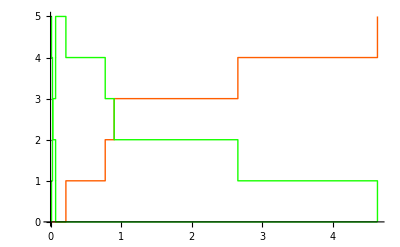

```mathematica
SSAPlot[sim]
```

#### Tabular Output

```mathematica
SSA[M1,50, ic, r, "Mode"-> "Table"]//TableForm
```

a0 = 0 at t=2.41751

xSSA Exit. 12 steps.  10 points sampled.  0.00181 seconds.

time | P | S | ℰ | S⋄ℰ
0 | 0 | 5 | 100 | 0
0.00633123 | 0 | 4 | 99 | 1
0.0241115 | 0 | 3 | 98 | 2
0.032952 | 0 | 2 | 97 | 3
0.0655528 | 0 | 1 | 96 | 4
0.0984399 | 0 | 0 | 95 | 5
0.140834 | 1 | 0 | 96 | 4
0.923016 | 2 | 0 | 97 | 3
1.00682 | 3 | 0 | 98 | 2
1.68324 | 4 | 0 | 99 | 1
2.41751 | 5 | 0 | 100 | 0

#### Interpolating Function

```mathematica
SSA[M1,50, ic, r, "Mode"-> "Interpolation"]
```

a0 = 0 at t=4.62338

xSSA Exit. 12 steps.  10 points sampled.  0.00201 seconds.

{P→InterpolatingFunction[{{0.,4.62338}},<>],S→InterpolatingFunction[{{0.,0.192978}},<>],ℰ→InterpolatingFunction[{{0.,4.62338}},<>],S⋄ℰ→InterpolatingFunction[{{0.,4.62338}},<>]}

#### Table of specific variables

```mathematica
SSA[M1,50, ic, r,  "Mode"-> "Variables", "Variables"-> {S,P}]
```

a0 = 0 at t=5.57975

xSSA Exit. 12 steps.  10 points sampled.  0.00171 seconds.

{{t,S,S ⋄ ℰ,P,P},{0,5,0,0,0},{0.0257458,4,1,0,0},{0.0389275,3,2,0,0},{0.0514128,2,3,0,0},{0.0584457,1,4,0,0},{0.0756175,0,5,0,0},{0.87223,0,4,1,1},{0.899427,0,3,2,2},{2.79927,0,2,3,3},{4.48976,0,1,4,4},{5.57975,0,0,5,5},{5.57975,0,0,5,5}}

## Stochastic Ring Oscillator

```mathematica
rings={{Underoverscript[X⇄XP, ZPP, Z],a,d,k,0, a,d,k, 0},
{Underoverscript[XP⇄XPP, ZPP, Z],a,d,k,0,a,d,k,0},{Underoverscript[Y⇄YP, XPP, X],a,d,k,0,a,d,k,0},{Underoverscript[YP⇄YPP, XPP, X],a,d,k,0,a,d,k,0},{Underoverscript[Z⇄ZP, YPP, Y],a,d,k,0,a,d,k,0},{Underoverscript[ZP⇄ZPP, YPP, Y],a,d,k,0,a,d,k,0}};
r={a-> 1, d-> 1, k-> 1};
IC={X-> 60, Y-> 40, Z-> 20};
```

```mathematica
sr=SSA[rings,100, IC, r, "Mode"-> "Interpolation"]
```

Warning:  the following variables are missing initial condtions, which are all assumed to be zero: {XP,XPP,YP,YPP,ZP,ZPP,X⋄Z,XP⋄Z,XP⋄ZPP,XPP⋄ZPP,Y⋄X,YP⋄X,YP⋄XPP,YPP⋄XPP,Z⋄Y,ZP⋄Y,ZP⋄YPP,ZPP⋄YPP}

xSSA Exit. 17015 steps.  17014 points sampled.  3.20768 seconds.

{X→InterpolatingFunction[{{0.,100.005}},<>],XP→InterpolatingFunction[{{0.,99.9604}},<>],XPP→InterpolatingFunction[{{0.,99.9837}},<>],Y→InterpolatingFunction[{{0.,99.9649}},<>],YP→InterpolatingFunction[{{0.,99.9697}},<>],YPP→InterpolatingFunction[{{0.,99.9837}},<>],Z→InterpolatingFunction[{{0.,100.005}},<>],ZP→InterpolatingFunction[{{0.,99.847}},<>],ZPP→InterpolatingFunction[{{0.,99.8823}},<>],X⋄Z→InterpolatingFunction[{{0.,100.005}},<>],XP⋄Z→InterpolatingFunction[{{0.,99.7104}},<>],XP⋄ZPP→InterpolatingFunction[{{0.,99.8823}},<>],XPP⋄ZPP→InterpolatingFunction[{{0.,99.8684}},<>],Y⋄X→InterpolatingFunction[{{0.,99.9649}},<>],YP⋄X→InterpolatingFunction[{{0.,99.9697}},<>],YP⋄XPP→InterpolatingFunction[{{0.,99.8726}},<>],YPP⋄XPP→InterpolatingFunction[{{0.,99.9837}},<>],Z⋄Y→InterpolatingFunction[{{0.,97.2069}},<>],ZP⋄Y→InterpolatingFunction[{{0.,97.3924}},<>],ZP⋄YPP→InterpolatingFunction[{{0.,99.847}},<>],ZPP⋄YPP→InterpolatingFunction[{{0.,99.5891}},<>]}

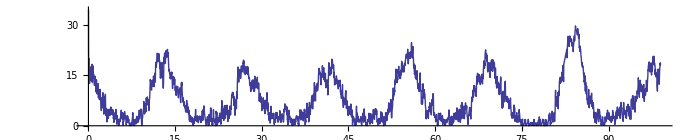

```mathematica
sp=Plot[X[t]/.sr, {t, 0, 99}, ImageSize->700, AspectRatio-> .2]
```

### Compare the single run with a single xlr8r run

```mathematica
<<xlr8r.m
```

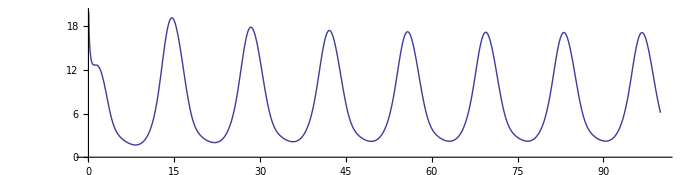

```mathematica
xr=run[rings, initialConditions-> IC, rates-> r];
xp=Plot[X[t]/.xr, {t, 0, 100}, PlotRange-> {0, 20}, ImageSize-> 700, AspectRatio-> .25]
```

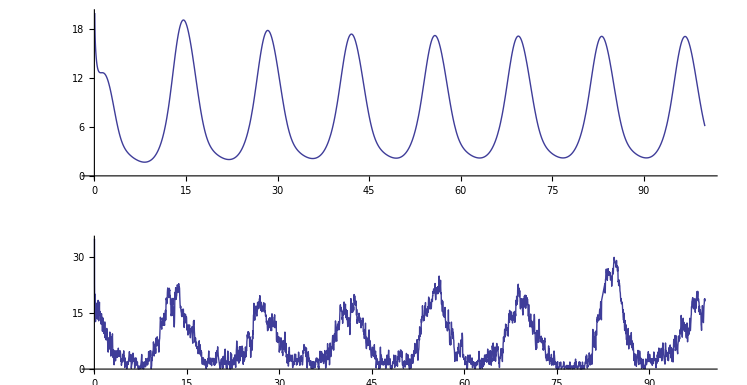

```mathematica
GraphicsColumn[{xp,sp}]
```